```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/home/elio/MEGA/gravEoS/JL

```mathematica
outputVideoName = "None" ;
```

```mathematica
prms = Import["OUTPUT/PARAMS.dat"];
m = prms[[1,1]]; r = prms[[1,2]];
xi = prms[[2,1]]; xf = prms[[2,2]];
yi = prms[[3,1]]; yf = prms[[3,2]];
zi = prms[[4,1]]; zf = prms[[4,2]];
nbp = prms[[5,1]]; lns = prms[[5,2]];
GG = prms[[6,1]]; σσ=prms[[6,2]]; ;
```

```mathematica
qqq = ConstantArray[0,{nbp,lns,5}];
For[i=1, i<=nbp, i++,
qqq[[i]]=Import[StringJoin["OUTPUT/particle",ToString[i],".dat"]];
]
```

```mathematica
Print[Style[Dimensions[qqq][[2]],20,Red]]
```

501

```mathematica
maxKinE = Max[qqq[[;;,;;,5]]];
{Round[maxKinE,1],maxKinE}
```

{205,205.21}

```mathematica
kinColor=ColorData["DarkRainbow"];
(*anm=Animate[
Canvas[
Graphics3D[Table[{kinColor[qqq[[i,st,5]]/Round[maxKinE,1]],Sphere[qqq[[i,st,2;;4]],r]},{i,1,nbp,1}],PlotRange->{{xi,xf},{yi,yf},{zi,zf}},ImageSize->600],
BarLegend[{"DarkRainbow",{0,Round[maxKinE,100]}},LegendLabel->"E_kin",LabelStyle->Directive[Black,FontSize->18]]
],
{st,1,Dimensions[qqq][[2]],1},ContinuousAction->False,DefaultDuration->60]*)
```

```mathematica
(*Export["tst.mp4",anm,ImageSize->{1920,1080},Antialiasing->True,CompressionLevel->0,DefaultDuration->60]*)
```

```mathematica
diamN2=0.32 10^-9;
volN2 = (4π)/3(diamN2/2)^3;
nAirSC=1.204/(4.81 10^-26);
nAirSC volN2 //ScientificForm
```

4.29467×10^-4

```mathematica
(nbp(4π)/3 r^3)/(Abs[zi-zf]Abs[yi-yf]Abs[yi-yf])//ScientificForm
```

3.927×10^-3

```mathematica
mnpl=Manipulate[
Canvas[
Graphics3D[Table[{kinColor[qqq[[i,st,5]]/maxKinE],Sphere[qqq[[i,st,2;;4]],r]},{i,1,nbp,1}],PlotRange->{{xi,xf},{yi,yf},{zi,zf}},ImageSize->600],
BarLegend[{"DarkRainbow",{0,Round[maxKinE,100]}},LegendLabel->"E_kin",LabelStyle->Directive[Black,FontSize->18]]
],
{st,1,Dimensions[qqq][[2]],1},
ContinuousAction->False,AutorunSequencing->0]
```

Table::iterb: Iterator {i,1,nbp,1} does not have appropriate bounds.

```mathematica
(*Export["mnpl.mp4",mnpl,ImageSize->{1920,1080},CompressionLevel->0,DefaultDuration->60]*)
```

```mathematica
If[outputVideoName!="None",

For[st=1,st<=Dimensions[qqq][[2]],st++,
Export[StringJoin["pics/st",IntegerString[st,10,4],".png"],
Rasterize[Canvas[
Graphics3D[Table[{kinColor[qqq[[i,st,5]]/Round[maxKinE,1]],Sphere[qqq[[i,st,2;;4]],r]},{i,1,nbp,1}],PlotRange->{{xi,xf},{yi,yf},{zi,zf}},ImageSize->600],
BarLegend[{"DarkRainbow",{0,Round[maxKinE,100]}},LegendLabel->"E_kin",LabelStyle->Directive[Black,FontSize->18]]
],ImageSize->400,ImageResolution->66]
]
];

Run[StringJoin["ffmpeg -y -framerate 10 -pattern_type glob -i 'pics/*.png' -c:v mpeg4 -q:v 2 ",outputVideoName,".avi"]];
Run["rm -r pics/*.png "];

]
```

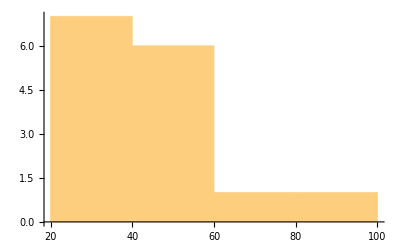

```mathematica
Histogram[qqq[[;;,Dimensions[qqq][[2]],5]]]
```

```mathematica
cnt=ConstantArray[0,lns];
For[stp=1,stp<=lns,stp++,
For[i=1,i<=nbp,i++,
For[j=i+1,j<=nbp,j++,
If[(qqq[[i,stp,5]]^2+qqq[[j,stp,5]]^2)/2- (GG m^2)/(√((qqq[[i,stp,2]]-qqq[[j,stp,2]])^2+(qqq[[i,stp,3]]-qqq[[j,stp,3]])^2+(qqq[[i,stp,4]]-qqq[[j,stp,4]])^2))<=0,cnt[[stp]]++]
]
]
]
```

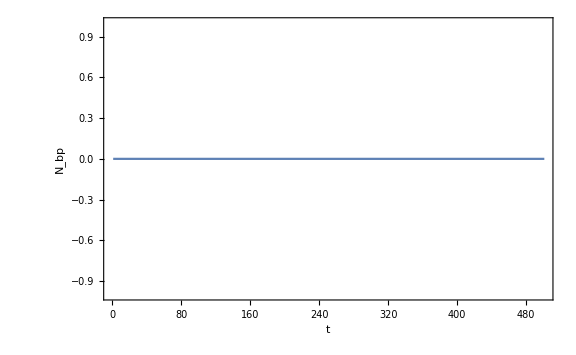

```mathematica
boundPairsImg=Show[
ListLinePlot[cnt,PlotRange->All,Frame->True,FrameStyle->Directive[Black,20,Thick],FrameLabel->{"t","N_bp"},ImageSize->Large]
]
```

```mathematica
bndClstrs = Import["OUTPUT/NbBoundClusters250_sigma1.5.dat"];
```

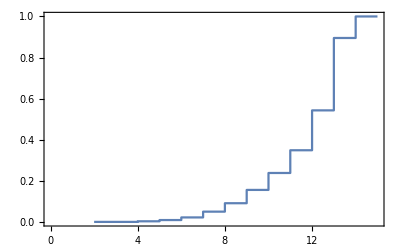

```mathematica
ListLinePlot[bndClstrs,InterpolationOrder->0,Frame->True]
```

```mathematica
bndClstrs
```

{{2,0.},{3,0.},{4,0.0029304},{5,0.00899101},{6,0.0217782},{7,0.0498834},{8,0.0909091},{9,0.155644},{10,0.238095},{11,0.348718},{12,0.542857},{13,0.895238},{14,1.},{15,1.}}

```mathematica
sig0d05={{2,0.},{3,0.01098901098901099},{4,0.05641025641025641},{5,0.14219114219114218},{6,0.3334665334665335},{7,0.6436674436674437},{8,0.9140637140637141},{9,0.9988011988011988},{10,1.},{11,1.},{12,1.},{13,1.},{14,1.},{15,1.}};
sig0d1={{2,0.},{3,0.002197802197802198},{4,0.0029304029304029304},{5,0.011322011322011322},{6,0.04095904095904096},{7,0.12183372183372183},{8,0.28438228438228436},{9,0.5394605394605395},{10,0.8271728271728271},{11,0.9897435897435898},{12,1.},{13,1.},{14,1.},{15,1.}};
sig0d5={{2,0.01904761904761905},{3,0.02197802197802198},{4,0.04981684981684982},{5,0.0979020979020979},{6,0.18541458541458541},{7,0.34265734265734266},{8,0.5797979797979798},{9,0.8335664335664336},{10,0.981018981018981},{11,1.},{12,1.},{13,1.},{14,1.},{15,1.}};
sig1={{2,0.01904761904761905},{3,0.054945054945054944},{4,0.07838827838827839},{5,0.12387612387612387},{6,0.1912087912087912},{7,0.2352758352758353},{8,0.2822066822066822},{9,0.4227772227772228},{10,0.5651015651015651},{11,0.7494505494505495},{12,0.9846153846153847},{13,1.},{14,1.},{15,1.}};
sig1d5={{2,0.},{3,0.},{4,0.0029304029304029304},{5,0.008991008991008992},{6,0.02177822177822178},{7,0.049883449883449886},{8,0.09090909090909091},{9,0.15564435564435564},{10,0.23809523809523808},{11,0.3487179487179487},{12,0.5428571428571428},{13,0.8952380952380953},{14,1.},{15,1.}};
sig2={{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.}};
sig5={{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.}};
```

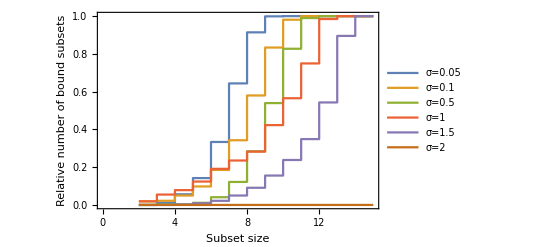

```mathematica
fg=ListLinePlot[{sig0d05,sig0d5,sig0d1,sig1,sig1d5,sig2},InterpolationOrder->0,Frame->True,FrameLabel->{"Subset size","Relative number of bound subsets"},PlotLegends->{"σ=0.05","σ=0.1","σ=0.5","σ=1","σ=1.5","σ=2"},FrameStyle->Directive[Black,Large],ImageSize->Full]
```

```mathematica
Export["bndSbsts.eps",fg]
```

bndSbsts.eps

```mathematica
bndClstrs1 = Import["OUTPUT/NbBoundClusters1_sigma1.8.dat"];
bndClstrs5 = Import["OUTPUT/NbBoundClusters5_sigma1.8.dat"];
bndClstrs10 = Import["OUTPUT/NbBoundClusters10_sigma1.8.dat"];
bndClstrs20= Import["OUTPUT/NbBoundClusters20_sigma1.8.dat"];
bndClstrs30 = Import["OUTPUT/NbBoundClusters30_sigma1.8.dat"];
bndClstrs40 = Import["OUTPUT/NbBoundClusters40_sigma1.8.dat"];
bndClstrs50 = Import["OUTPUT/NbBoundClusters50_sigma1.8.dat"];
bndClstrs70 = Import["OUTPUT/NbBoundClusters70_sigma1.8.dat"];
bndClstrs90 = Import["OUTPUT/NbBoundClusters90_sigma1.8.dat"];
bndClstrs120 = Import["OUTPUT/NbBoundClusters120_sigma1.8.dat"];
bndClstrs200 = Import["OUTPUT/NbBoundClusters200_sigma1.8.dat"];
bndClstrs250 = Import["OUTPUT/NbBoundClusters250_sigma1.8.dat"];
bndClstrs300 = Import["OUTPUT/NbBoundClusters300_sigma1.8.dat"];
bndClstrs400 = Import["OUTPUT/NbBoundClusters400_sigma1.8.dat"];
bndClstrs500 = Import["OUTPUT/NbBoundClusters500_sigma1.8.dat"];
```

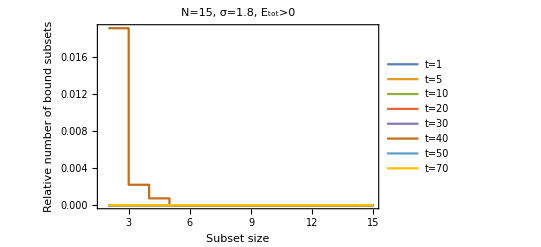

```mathematica
fgTime1=ListLinePlot[{bndClstrs1,bndClstrs5,bndClstrs10,bndClstrs20,bndClstrs30,bndClstrs40,bndClstrs50,bndClstrs70},InterpolationOrder->0,PlotRange->All,Frame->True,FrameLabel->{"Subset size","Relative number of bound subsets"},PlotLegends->{"t=1","t=5","t=10","t=20","t=30","t=40","t=50","t=70"},FrameStyle->Directive[Black,Large],ImageSize->Full,PlotLabel->"N=15, σ=1.8, E_tot>0"]
```

```mathematica
"t=90","t=120","t=200"
```

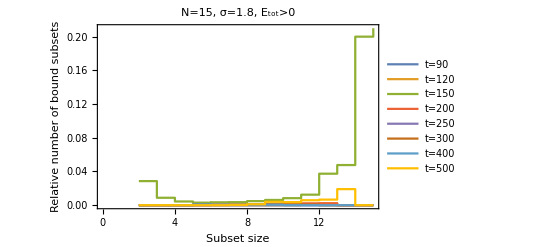

```mathematica
fgTime2=ListLinePlot[{bndClstrs90,bndClstrs120,bndClstrs150,bndClstrs200,bndClstrs250,bndClstrs300,bndClstrs400,bndClstrs500},PlotRange->{0,0.21},InterpolationOrder->0,Frame->True,FrameLabel->{"Subset size","Relative number of bound subsets"},PlotLegends->{"t=90","t=120","t=150","t=200","t=250","t=300","t=400","t=500"},FrameStyle->Directive[Black,Large],ImageSize->Full,PlotLabel->"N=15, σ=1.8, E_tot>0"]
```

```mathematica
Export["bndSbstsTime1.eps",fgTime1]
Export["bndSbstsTime2.eps",fgTime2]
```

bndSbstsTime1.eps

bndSbstsTime2.eps